# Symbolic Diff Tools for Opt

We have a bunch of variable dimensioned functions and I want to automate building symbolic 1st and 2nd derivatives.  I also want to think about automating some sort of assessment of their degree of difficulty in terms of: how many saddles there are; the index of the saddles; the relative sizes of the Hessian eigenvalues at the critical points, etc.  I am going to try to do this on a rectangular region surrounding the proposed starting point.

I am going to test on the generalized Rosenbrock function.

### Generalized Rosenbrock Function

```mathematica
Rosen[x_]:=Module[{n=Length[x],c=100.0},
Sum[
c (x⟦i+1⟧-x⟦i⟧^2)^2+(1.0-x⟦i⟧)^2,
{i,1,n-1}]
]
```

### Auto Diff Tool

The evaluates are needed to get the correct expressions into the constructed functions. Quiet is needed to prevent it from complaining about trying to access entries of non-assigned object.

```mathematica
BuildGradAndHess[f_,n_]:= Module[
{x,i,var,df,ddf},
var=Array[x,n];
df=D[f[var],{var}];
ddf=D[f[var],{var,2}];
Quiet[
{Function[Evaluate[x],Evaluate[df/.x[i_]:>Part[x,i]]],
Function[Evaluate[x],Evaluate[ddf/.x[i_]:>Part[x,i]]]}
]
]
```

```mathematica
n=12;
f=Rosen;
{df,ddf}=BuildGradAndHess[f,n];
x0=RandomReal[{-1,1},n];
u=Normalize[RandomReal[{-1,1},n]];
Taylor[t_]=f[x0]+(df[x0].u) t+(u.ddf[x0].u)t^2/2.0;
TabView[{
"Eyeball"->Plot[ {Rosen[x0+t u],Taylor[t]} ,{t, -1,1}],
"Error"->LogLogPlot[ {
t^3,
Abs[Rosen[x0+t u]-Taylor[t]],
Abs[Rosen[x0-t u]-Taylor[-t]]
} ,{t, 10^-12,0.1},
PlotLegends->{"t^3","+t","-t"},
PlotRange->All,
GridLines->Automatic]
}]
```

12

### Box Sample Construction

I think all the test problems come with a suggested start value and are defined on all of ℝ^n.  At lest some of the start values contain a range of scales. My sampling box for a given initial point z_(1:n) is going to be
	𝔹={x∈ℝ^n: -R_i≤x_i≤ R_i}
where R_i=2Abs[z_i] provided z_i≠0 and R_i=1 if Abs[z_i]<Tol.

```mathematica
SampleFromBox[z_,s_Integer]:= Module[{n=Length[z],Tol=0.1,Scale},
Scale=2.0*Abs[z];
Do[If[Scale⟦i⟧≤2.0*Tol,Scale⟦i⟧=1],{i,1,n}];
Table[
RandomReal[{-1,1},n]*Scale,
{s}]
]
```

```mathematica
ListPointPlot3D[SampleFromBox[{1,2,0},1245]]
```

-Graphics3D-

### Random Search for Critical Points

Run a critical point finder on a sample of starting points

```mathematica
{n,s}={4,23};
f=Rosen;
{df,ddf}=BuildGradAndHess[f,n];
z=ConstantArray[1.0,n];z⟦-1⟧=-1.0;
S=SampleFromBox[z,s];
Clear[x]
vars=Array[x,n];
i=2;
FindRootOutput=Table[
Quiet[vars/.FindRoot[df[vars],{vars, S⟦i⟧}ᵀ]],
{i,1,s}];
Map[f,FindRootOutput]
Map[Norm,Map[df,FindRootOutput]]
```

{0.,3.31568×10^-30,3.70824,1.2326×10^-30,3.13296,2.52682×10^-30,1.49144×10^-30,4.37571×10^-30,2.82264×10^-30,1.2326×10^-30,3.70143,3.70143,3.70143,1.30655×10^-30,1.24492×10^-30,0.,1.2326×10^-30,0.,3.70778,0.,0.,0.,1.2326×10^-30}

{0.,8.23271×10^-14,1.01584×10^-14,4.96507×10^-14,6.52608,7.05686×10^-14,4.88604×10^-14,8.3246×10^-14,4.98138×10^-14,4.96507×10^-14,2.81743×10^-15,3.53899×10^-14,5.19157×10^-14,4.97529×10^-14,4.97504×10^-14,0.,4.96507×10^-14,0.,0.928943,0.,0.,0.,4.96507×10^-14}

{{{34,0,12},1},{{35,0,11},2},{{36,0,10},3},{{37,0,9},14},{{38,0,8},28},{{39,0,7},72},{{40,0,6},91},{{41,0,5},81},{{42,0,4},61},{{43,0,3},44},{{44,0,2},18},{{45,0,1},6},{{46,0,0},2}}

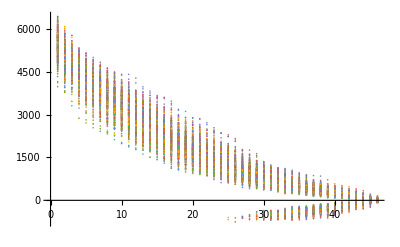

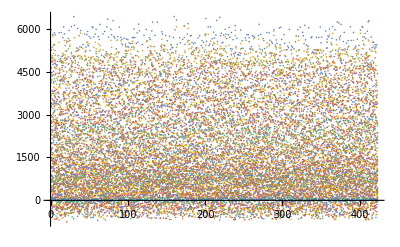

```mathematica
{n,s}={46,423};
f=Rosen;
{df,ddf}=BuildGradAndHess[f,n];
z=ConstantArray[1.0,n];z⟦-1⟧=-1.0;
S=SampleFromBox[z,s];
SampledEvals=Table[ Eigenvalues[ddf[S⟦i⟧]],{i,1,s}];
Index[λs_]:= Module[{Indicator=Sign[λs]},
{Count[Indicator,1],Count[Indicator,0],Count[Indicator,-1]}]
Sort[Tally[Map[Index,SampledEvals]]]
ListPlot[SampledEvals]
ListPlot[SampledEvalsᵀ]
```